Compile the NDSolve parameter sweep

```mathematica
lorenz=Compile[
{{parameterList,_Real,1}},
Table[
counter=0;
sol=NDSolve[
{
x'[t]==10(y[t-13/28]-x[t]),
y'[t]==parameterList[[i]]*x[t] - y[t] - z[t]*x[t],
z'[t]==x[t]*y[t]-8/3  z[t],
x[t/;t≤0]==-8,
y[t/;t≤0]== -8+Sin[2π t],
z[t/;t≤0]==-8
},
x[t],
{t,0,10},
Method->{"ExplicitRungeKutta","DifferenceOrder"->5},
StartingStepSize->0.01,
MaxSteps->10100,
PrecisionGoal->8,
AccuracyGoal->8,
StepMonitor:>counter++
];
{First@Evaluate[x[t]/.sol]/.t->10,counter},
{i,1,Length[parameterList]}],
CompilationTarget->"C",
"RuntimeOptions"->"Speed"
]
```

CompiledFunction[…]

Run and Benchmark

```mathematica
nrOfParameters = 128;
parameterList =N@Range[0,50,50/(nrOfParameters-1)];
runtime=Timing[endvals=lorenz[parameterList]];
runtime[[1]]
```

6.04688

Export endvals

```mathematica
SetDirectory[NotebookDirectory[]];
Export["lorenz_endvals.txt",data=Transpose[{parameterList,endvals[[All,1]],endvals[[All,2]]}],"Table"]
```

lorenz_endvals.txt

Plot endvals

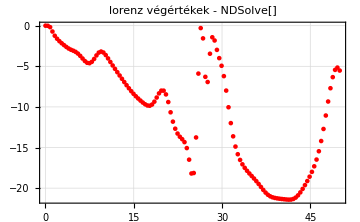

```mathematica
plt=Show[
(*Plot[Evaluate[x[p][10]/.logistic1EndValues],{p,0,2},PlotStyle->Blue],*)
ListPlot[
data[[All,{1,2}]],
PlotStyle->Red,
FrameLabel->(MaTeX[#,Magnification->1.2]&)/@{"p","x(10)"},
PlotLabel->Style["lorenz végértékek - NDSolve[]",Black,14]
]
]
(*Export["lorenz_endvals.png",plt,ImageResolution->1000]*)
```